Mixing, χ^2 = 8.9216

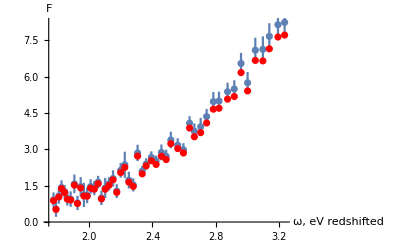

```mathematica
(*Clear["Global`*"]*)

Needs["ErrorBarPlots`"]
dat =Import["C:\\Users\\Алексей\\Documents\\Kulkarni.dat"];
dTransposed=Transpose[dat];
dAngst=dTransposed[[1]];
deVUnreversed= 2 Pi/#*1.97*10^3&/@dAngst;
dTransposed[[1]]=deVUnreversed;
spectrumData=Reverse[dTransposed[[2]]];
deVReversed=Reverse[deVUnreversed];
errorData=Reverse[dTransposed[[3]]];

kulkarniPlot=ErrorListPlot[{{#1,#2},ErrorBar[#3]}&@@@Transpose[dTransposed],AxesLabel->{"ω, eV\nredshifted","F"}];

datMixing=Import["C:\\Users\\Алексей\\Documents\\Mixing_m_t4_p-6__g_t6_p-20.dat"];
modificationFactor=Transpose[datMixing][[2]];
mixedSpectrum=spectrumData*modificationFactor;

mixedPlot=ListPlot[Transpose[{deVReversed,mixedSpectrum}],PlotStyle->Red];



(*Хи квадрат с погрешностями*)
chiTestError:=Function[{spectrum,mixed,error},(spectrum-mixed)^2/((error)^2+(0.054*spectrum)^2)];

lB:=1;
rB:=49;

Print["Mixing, χ^2 = ",Total[chiTestError@@@Transpose[{spectrumData[[lB;;rB]],mixedSpectrum[[lB;;rB]],errorData[[lB;;rB]]}]]];

Show[kulkarniPlot,mixedPlot]
```

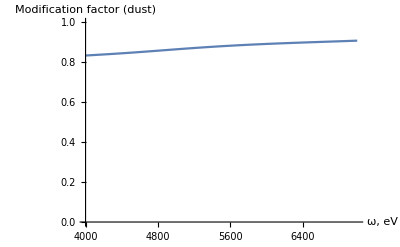

```mathematica
(*Поглощение на пыли*)

(*Коэффициенты кривой поглощения*)

Fa[x_]:=Piecewise[ {{-0.04473(x-5.9)^2-0.009779(x-5.9)^3, 5.9≤x≤8}},
0];
Fb[x_]:=Piecewise[ {{0.2130(x-5.9)^2+0.1207(x-5.9)^3, 5.9≤x≤8}},
0];

a[x_]:=Piecewise[{
{0.574 x^(1.61),0.3<x≤1.1},
	{1+0.104*(x-1.82)-0.609*(x-1.82)^2+0.701*(x-1.82)^3+1.137*(x-1.82)^4-1.718*(x-1.82)^5-0.827*(x-1.82)^6+1.647*(x-1.82)^7-0.505*(x-1.82)^8,1.1<=x<3.3},
{1.752-0.316x-0.104/((x-4.67)^2+0.341)+Fa[x],3.3<=x<8},
{-1.073-0.628(x-8)+0.137(x-8)^2-0.070(x-8)^3,8≤x<10}},
	0];
b[x_]:=Piecewise[{
{-0.527  x^(1.61),0.3<x≤1.1},
	{1.952*(x-1.82)+2.908*(x-1.82)^2-3.989*(x-1.82)^3-7.985*(x-1.82)^4+11.102*(x-1.82)^5+5.491*(x-1.82)^6-10.805*(x-1.82)^7+3.347*(x-1.82)^8,1.1<=x<3.3},
{-3.090+1.825x+1.206/((x-4.62)^2+0.263)+Fb[x],3.3<=x<8},
{13.670+4.257(x-8)-0.420(x-8)^2+0.374(x-8)^3,8≤x<10}},
0];
Rv:=3.1;
Av:=0.138;
extinctionCurveDustMkMeters[mkM_]:=10^(-0.4*Av*(a[mkM]+b[mkM]/Rv ));
extinctionCurveDustMkMeters1[mkM_]:=a[mkM]+b[mkM]/Rv;
extinctionCurveDustEv[eV_]:=extinctionCurveDustMkMeters[eV*0.197]
extinctionCurveDustAngst[Angst_]:=extinctionCurveDustMkMeters[1/(0.0001*Angst)]
Plot[extinctionCurveDustAngst[x],{x,4000,7000},AxesLabel->{"ω, eV","Modification factor (dust)"},PlotRange->{{All,All},{0,1}}]
```

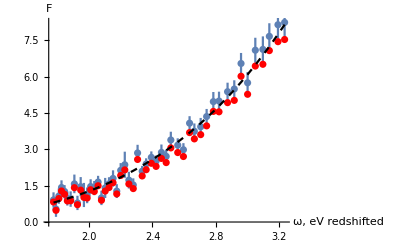

```mathematica
fFit[lambda_]:=f0*(lambda/lambda0)^(-4)*extinctionCurveDustAngst[lambda];
f0:=3.36;
lambda0:=5000;
fitDataAngst=fFit/@dAngst;
fitDataEv=Reverse[fitDataAngst];
fitPlot=ListLinePlot[Transpose[{deVReversed,fitDataEv}],PlotStyle->{Dashed,Black}];
Show[kulkarniPlot,mixedPlot,fitPlot]
```

```mathematica
chiTestError:=Function[{spectrum,mixed,error},(spectrum-mixed)^2/((error)^2+(0.054*spectrum)^2)];

lB:=1;
rB:=49;
Print["Fit, χ^2 = ",Total[chiTestError@@@Transpose[{spectrumData[[lB;;rB]],fitDataEv[[lB;;rB]],errorData[[lB;;rB]]}]]];
Print["Mixing, χ^2 = ",Total[chiTestError@@@Transpose[{spectrumData[[lB;;rB]],mixedSpectrum[[lB;;rB]],errorData[[lB;;rB]]}]]];
```

Fit, χ^2 = 37.3248

Mixing, χ^2 = 23.8687

```mathematica
spectrumData[[lB;;rB]]
fitDataEv[[lB;;rB]]
errorData[[lB;;rB]]
#2/#1&@@@Transpose[{spectrumData[[lB;;rB]],errorData[[lB;;rB]]}]//Mean
```

{0.913617,0.534638,1.06989,1.4266,1.26184,0.968558,0.946635,1.57466,0.788503,1.45948,1.11618,1.10146,1.46528,1.40053,1.65005,0.995348,1.40632,1.5773,1.7997,1.27642,2.13313,2.36412,1.72941,1.53181,2.85138,2.09665,2.39627,2.67007,2.51535,2.87488,2.71162,3.38837,3.17352,2.9845,4.08117,3.74652,3.93463,4.35421,4.97089,4.99623,5.38139,5.4924,6.54627,5.74874,7.09401,7.12788,7.66753,8.14707,8.24102}

{0.812571,0.840873,0.874325,0.906798,0.944937,0.980698,1.02438,1.07556,1.11933,1.16648,1.21502,1.26514,1.32111,1.38124,1.44604,1.50518,1.57308,1.64476,1.72228,1.79668,1.87742,1.96458,2.05431,2.15395,2.25521,2.3669,2.46652,2.60069,2.72816,2.87715,3.01484,3.15388,3.36912,3.55491,3.76419,3.93327,4.16576,4.39338,4.66213,4.89873,5.27288,5.58164,5.90656,6.23567,6.63972,7.05429,7.42363,7.93749,8.35124}

{0.311413,0.321386,0.31716,0.29428,0.26138,0.288552,0.318565,0.38426,0.295707,0.39571,0.49857,0.32429,0.29998,0.29286,0.25713,0.297152,0.41426,0.27146,0.33433,0.28569,0.30003,0.53997,0.34573,0.27141,0.33714,0.21998,0.23421,0.24566,0.22857,0.32573,0.27429,0.33997,0.28288,0.27144,0.28864,0.32285,0.36287,0.31429,0.39716,0.38573,0.37144,0.35996,0.43429,0.44571,0.51428,0.53718,0.53999,0.57431,0.60855}

0.174006